# Les polynômes orthogonales

## Formule de Rodrigues - Les polynômes de Hermite H_n(x)

```mathematica
Clear["Global`*"]
```

Les polynômes de Hermite, notés H_n(x)sont, H_0(x),H_1(x),H_2(x),...,H_k(x).

## Formule de Rodrigues

Les polynômes de Hermite peut être définie par la formule de Rodrigues :

```mathematica
H[n_,x_]:=1/(K[n] w[x])D[(w[x] g[x]^n), {x,n}]
```

### Initiation

```mathematica
table={{"Polynôme de degré 0, 1, ou 2", g[x_]=1}, {"Fonction poids", w[x_]=ⅇ^(-x^2)}, {"Limite gauche d'intervalle d'orthogonalité", a=-∞}, {"Limite droite d'intervalle d'orthogonalité", b=+∞}, {"Multiplicateur de standardisation", K[n_]=(-1)^n}, {"Coefficient de x", κ[n_]=2^n}, {"Ordre", k:=3}};
```

## Les polynômes

```mathematica
TableForm[Table[{n,H[n,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","H[n,x]"}}]
```

n | H[n,x]
0 | 1
1 | 2 x
2 | -2+4 x^2
3 | 4 x (-3+2 x^2)

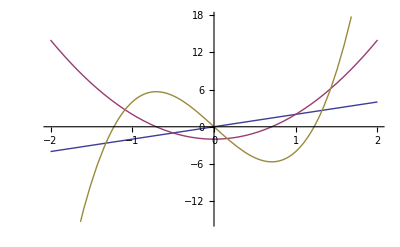

```mathematica
Plot[Evaluate[Table[H[n,x],{n,k}]],{x,-2,2}]
```

## Orthogonalité

```mathematica
Table[∫_a^b w[x]H[n,x] H[n',x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

√π | 0 | 0 | 0
0 | 2 √π | 0 | 0
0 | 0 | 8 √π | 0
0 | 0 | 0 | 48 √π

#### Carré de la norme

```mathematica
h[n_]=((-1)^n κ[n]n!)/K[n]∫_a^b w[x] g[x]^n ⅆx
```

2^n √π n!

```mathematica
Table[h[n]KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

√π | 0 | 0 | 0
0 | 2 √π | 0 | 0
0 | 0 | 8 √π | 0
0 | 0 | 0 | 48 √π

## Normalization

```mathematica
H̃[n_,x_]:=H[n,x]/(√h[n])
```

```mathematica
TableForm[Table[{n,H̃[n,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,3},TableHeadings->{None,{"n","H̃[n,x]"}}]
```

n | H̃[n,x]
0 | 1/π^(1/4)
1 | (√2 x)/π^(1/4)
2 | (-1+2 x^2)/(√2 π^(1/4))
3 | (x (-3+2 x^2))/(√3 π^(1/4))

## Orthonormalité

```mathematica
Table[∫_a^b w[x]H̃[n,x]H̃[n',x]ⅆx,{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
Table[KroneckerDelta[n,n'],{n,0,k},{n',0,k}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

## Développement de la fonction f(x)

### La fonction à développer

```mathematica
f[x_] := Sin[x]
```

### Les coéfficients

```mathematica
Subscript[a, n_]:=∫_a^b w[x]H̃[n,x]f[x]ⅆx
```

```mathematica
Table[Subscript[a, n],{n,0,k}]
```

{0,(π/ⅇ)^(1/4)/(√2),0,-(π/ⅇ)^(1/4)/(4 √3)}

### Développement

```mathematica
fdev[x_]:=∑_(n=0)^5 Subscript[a, n] H̃[n,x]
```

## Représentation

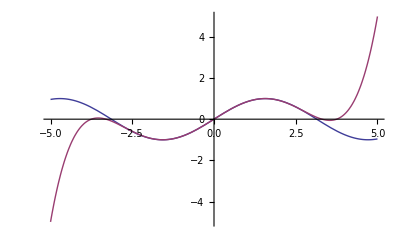

```mathematica
Plot[Evaluate[{f[x],fdev[x]}],{x,-5,5},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[{f[x],∑_(n=0)^k Subscript[a, n] H̃[n,x]}],{x,-5,5},PlotRange->All],{k,1,10,1},ControlType->Setter]
```

## EDP

```mathematica
λ[n_]=n(K[1]D[H[1,x], {x,1}]+1/2(n-1)D[g[x], {x,2}])//FullSimplify
```

-2 n

Le n - ième polynôme de Laguerre satisfait l' équation différentielle suivante :

```mathematica
EDP=(D[(w[x] g[x]D[u[x], x]), x]-λ[n] w[x]u[x])/w[x]==0//FullSimplify
```

2 n u[x]+u''[x]==2 x u'[x]

```mathematica
DSolve[EDP,u[x],x]
```

{{u[x]→C[1] HermiteH[n,x]+C[2] Hypergeometric1F1[-n/2,1/2,x^2]}}

```mathematica
TableForm[Table[{n,H[n,x],HermiteH[n,x]},{n,0,k}]//Simplify,TableAlignments->Left,TableSpacing->{3,5},TableHeadings->{None,{"n","H[n,x]","HermiteH[n,x]"}}]
```

n | H[n,x] | HermiteH[n,x]
0 | 1 | 1
1 | 2 x | 2 x
2 | -2+4 x^2 | -2+4 x^2
3 | 4 x (-3+2 x^2) | 4 x (-3+2 x^2)